```mathematica
a=({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, -((Pi^2)/288), 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, -((Pi^2)/288), 1, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, -((Pi^2)/288), 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1, -((Pi^2)/288), 1, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -((Pi^2)/288), 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, -((Pi^2)/288), 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, -((Pi^2)/288), 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, -((Pi^2)/288), 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, -((Pi^2)/288), 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -((Pi^2)/288), 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -((Pi^2)/288), 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}})
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0},{1,-π^2/288,1,0,0,0,0,0,0,0,0,0,0},{0,1,-π^2/288,1,0,0,0,0,0,0,0,0,0},{0,0,1,-π^2/288,1,0,0,0,0,0,0,0,0},{0,0,0,1,-π^2/288,1,0,0,0,0,0,0,0},{0,0,0,0,1,-π^2/288,1,0,0,0,0,0,0},{0,0,0,0,0,1,-π^2/288,1,0,0,0,0,0},{0,0,0,0,0,0,1,-π^2/288,1,0,0,0,0},{0,0,0,0,0,0,0,1,-π^2/288,1,0,0,0},{0,0,0,0,0,0,0,0,1,-π^2/288,1,0,0},{0,0,0,0,0,0,0,0,0,1,-π^2/288,1,0},{0,0,0,0,0,0,0,0,0,0,1,-π^2/288,1},{0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
b=({{0}, {((Pi^2)/2304)*Cos[Pi/48]}, {((Pi^2)/2304)*Cos[Pi/24]}, {((Pi^2)/2304)*Cos[Pi/16]}, {((Pi^2)/2304)*Cos[Pi/12]}, {((Pi^2)/2304)*Cos[(5*Pi)/48]}, {((Pi^2)/2304)*Cos[Pi/8]}, {((Pi^2)/2304)*Cos[(7*Pi)/48]}, {((Pi^2)/2304)*Cos[Pi/6]}, {((Pi^2)/2304)*Cos[(3*Pi)/16]}, {((Pi^2)/2304)*Cos[(5*Pi)/24]}, {((Pi^2)/2304)*Cos[(11*Pi)/48]}, {0}})
```

{{0},{(π^2 Cos[π/48])/2304},{(π^2 Cos[π/24])/2304},{(π^2 Cos[π/16])/2304},{((1+√3) π^2)/(4608 √2)},{(π^2 Cos[(5 π)/48])/2304},{(π^2 Cos[π/8])/2304},{(π^2 Cos[(7 π)/48])/2304},{π^2/(1536 √3)},{(π^2 Cos[(3 π)/16])/2304},{(π^2 Cos[(5 π)/24])/2304},{(π^2 Cos[(11 π)/48])/2304},{0}}

```mathematica
LinearSolve[a,b]
```

{{0},{(13631146639813244878848 √2 π^2+13631146639813244878848 √3 π^2+13631146639813244878848 √6 π^2-410853908655636480 √2 π^6-82170781731127296 √3 π^6-410853908655636480 √6 π^6+2972033482752 √2 π^10+2972033482752 √6 π^10-5971968 √2 π^14-5971968 √6 π^14+3925770232266214525108224 Cos[π/48]-709955554156939837440 π^4 Cos[π/48]+19972065004093440 π^8 Cos[π/48]-192631799808 π^12 Cos[π/48]+746496 π^16 Cos[π/48]-π^20 Cos[π/48]-68155733199066224394240 π^2 Cos[π/24]+3286831269245091840 π^6 Cos[π/24]-41608468758528 π^10 Cos[π/24]+191102976 π^14 Cos[π/24]-288 π^18 Cos[π/24]-3925770232266214525108224 Cos[π/16]+473303702771293224960 π^4 Cos[π/16]-8559456430325760 π^8 Cos[π/16]+48157949952 π^12 Cos[π/16]-82944 π^16 Cos[π/16]+3925770232266214525108224 Cos[(5 π)/48]-283982221662775934976 π^4 Cos[(5 π)/48]+2853152143441920 π^8 Cos[(5 π)/48]-6879707136 π^12 Cos[(5 π)/48]-40893439919439734636544 π^2 Cos[π/8]+657366253849018368 π^6 Cos[π/8]-1981355655168 π^10 Cos[π/8]-3925770232266214525108224 Cos[(7 π)/48]+141991110831387967488 π^4 Cos[(7 π)/48]-570630428688384 π^8 Cos[(7 π)/48]+3925770232266214525108224 Cos[(3 π)/16]-47330370277129322496 π^4 Cos[(3 π)/16]-13631146639813244878848 π^2 Cos[(5 π)/24]-3925770232266214525108224 Cos[(11 π)/48])/(8 (-23554621393597287150649344+1656562959699526287360 π^4-31955304006549504 π^8+247669456896 π^12-829440 π^16+π^20))},{(47330370277129322496 √2 π^4+47330370277129322496 √3 π^4+47330370277129322496 √6 π^4-1426576071720960 √2 π^8-285315214344192 √3 π^8-1426576071720960 √6 π^8+10319560704 √2 π^12+10319560704 √6 π^12-20736 √2 π^16-20736 √6 π^16-68155733199066224394240 π^2 Cos[π/48]+3286831269245091840 π^6 Cos[π/48]-41608468758528 π^10 Cos[π/48]+191102976 π^14 Cos[π/48]-288 π^18 Cos[π/48]-236651851385646612480 π^4 Cos[π/24]+11412608573767680 π^8 Cos[π/24]-144473849856 π^12 Cos[π/24]+663552 π^16 Cos[π/24]-π^20 Cos[π/24]-13631146639813244878848 π^2 Cos[π/16]+1643415634622545920 π^6 Cos[π/16]-29720334827520 π^10 Cos[π/16]+167215104 π^14 Cos[π/16]-288 π^18 Cos[π/16]+13631146639813244878848 π^2 Cos[(5 π)/48]-986049380773527552 π^6 Cos[(5 π)/48]+9906778275840 π^10 Cos[(5 π)/48]-23887872 π^14 Cos[(5 π)/48]-141991110831387967488 π^4 Cos[π/8]+2282521714753536 π^8 Cos[π/8]-6879707136 π^12 Cos[π/8]-13631146639813244878848 π^2 Cos[(7 π)/48]+493024690386763776 π^6 Cos[(7 π)/48]-1981355655168 π^10 Cos[(7 π)/48]+13631146639813244878848 π^2 Cos[(3 π)/16]-164341563462254592 π^6 Cos[(3 π)/16]-47330370277129322496 π^4 Cos[(5 π)/24]-13631146639813244878848 π^2 Cos[(11 π)/48])/(8 (-23554621393597287150649344+1656562959699526287360 π^4-31955304006549504 π^8+247669456896 π^12-829440 π^16+π^20))},{(164341563462254592 √2 π^2+164341563462254592 √3 π^2+164341563462254592 √6 π^2-4953389137920 √2 π^6-990677827584 √3 π^6-4953389137920 √6 π^6+35831808 √2 π^10+35831808 √6 π^10-72 √2 π^14-72 √6 π^14+47330370277129322496 Cos[π/48]-5135673858195456 π^4 Cos[π/48]+41278242816 π^8 Cos[π/48]-82944 π^12 Cos[π/48]+164341563462254592 π^2 Cos[π/24]-17832200896512 π^6 Cos[π/24]+143327232 π^10 Cos[π/24]-288 π^14 Cos[π/24]-47330370277129322496 Cos[π/16]+5706304286883840 π^4 Cos[π/16]-103195607040 π^8 Cos[π/16]+580608 π^12 Cos[π/16]-π^16 Cos[π/16]+47330370277129322496 Cos[(5 π)/48]-3423782572130304 π^4 Cos[(5 π)/48]+34398535680 π^8 Cos[(5 π)/48]-82944 π^12 Cos[(5 π)/48]-493024690386763776 π^2 Cos[π/8]+7925422620672 π^6 Cos[π/8]-23887872 π^10 Cos[π/8]-47330370277129322496 Cos[(7 π)/48]+1711891286065152 π^4 Cos[(7 π)/48]-6879707136 π^8 Cos[(7 π)/48]+47330370277129322496 Cos[(3 π)/16]-570630428688384 π^4 Cos[(3 π)/16]-164341563462254592 π^2 Cos[(5 π)/24]-47330370277129322496 Cos[(11 π)/48])/(8 (283982221662775934976-16548282431963136 π^4+185752092672 π^8-746496 π^12+π^16))},{(2282521714753536 √2 π^4+2282521714753536 √3 π^4+2282521714753536 √6 π^4-68797071360 √2 π^8-13759414272 √3 π^8-68797071360 √6 π^8+497664 √2 π^12+497664 √6 π^12-√2 π^16-√6 π^16-1314732507698036736 π^2 Cos[π/48]+31701690482688 π^6 Cos[π/48]-95551488 π^10 Cos[π/48]-4565043429507072 π^4 Cos[π/24]+110075314176 π^8 Cos[π/24]-331776 π^12 Cos[π/24]+1314732507698036736 π^2 Cos[π/16]-47552535724032 π^6 Cos[π/16]+477757440 π^10 Cos[π/16]-1152 π^14 Cos[π/16]+657366253849018368 π^2 Cos[(5 π)/48]-47552535724032 π^6 Cos[(5 π)/48]+477757440 π^10 Cos[(5 π)/48]-1152 π^14 Cos[(5 π)/48]-6847565144260608 π^4 Cos[π/8]+110075314176 π^8 Cos[π/8]-331776 π^12 Cos[π/8]-657366253849018368 π^2 Cos[(7 π)/48]+23776267862016 π^6 Cos[(7 π)/48]-95551488 π^10 Cos[(7 π)/48]+657366253849018368 π^2 Cos[(3 π)/16]-7925422620672 π^6 Cos[(3 π)/16]-2282521714753536 π^4 Cos[(5 π)/24]-657366253849018368 π^2 Cos[(11 π)/48])/(32 (141991110831387967488-9130086859014144 π^4+137594142720 π^8-663552 π^12+π^16))},{(-6815573319906622439424 √2 π^2+13631146639813244878848 √3 π^2-6815573319906622439424 √6 π^2+534110081252327424 √2 π^6-575195472117891072 √3 π^6+534110081252327424 √6 π^6-7925422620672 √2 π^10+4953389137920 √3 π^10-7925422620672 √6 π^10+41803776 √2 π^14-11943936 √3 π^14+41803776 √6 π^14-72 √2 π^18-72 √6 π^18+3925770232266214525108224 Cos[π/48]-283982221662775934976 π^4 Cos[π/48]+2853152143441920 π^8 Cos[π/48]-6879707136 π^12 Cos[π/48]+13631146639813244878848 π^2 Cos[π/24]-986049380773527552 π^6 Cos[π/24]+9906778275840 π^10 Cos[π/24]-23887872 π^14 Cos[π/24]-3925770232266214525108224 Cos[π/16]+331312591939905257472 π^4 Cos[π/16]-6276934715572224 π^8 Cos[π/16]+41278242816 π^12 Cos[π/16]-82944 π^16 Cos[π/16]+3925770232266214525108224 Cos[(5 π)/48]-425973332494163902464 π^4 Cos[(5 π)/48]+13695130288521216 π^8 Cos[(5 π)/48]-151353556992 π^12 Cos[(5 π)/48]+663552 π^16 Cos[(5 π)/48]-π^20 Cos[(5 π)/48]-40893439919439734636544 π^2 Cos[π/8]+2136440325009309696 π^6 Cos[π/8]-31701690482688 π^10 Cos[π/8]+167215104 π^14 Cos[π/8]-288 π^18 Cos[π/8]-3925770232266214525108224 Cos[(7 π)/48]+283982221662775934976 π^4 Cos[(7 π)/48]-6276934715572224 π^8 Cos[(7 π)/48]+41278242816 π^12 Cos[(7 π)/48]-82944 π^16 Cos[(7 π)/48]+3925770232266214525108224 Cos[(3 π)/16]-189321481108517289984 π^4 Cos[(3 π)/16]+2282521714753536 π^8 Cos[(3 π)/16]-6879707136 π^12 Cos[(3 π)/16]-13631146639813244878848 π^2 Cos[(5 π)/24]+493024690386763776 π^6 Cos[(5 π)/24]-1981355655168 π^10 Cos[(5 π)/24]-3925770232266214525108224 Cos[(11 π)/48]+141991110831387967488 π^4 Cos[(11 π)/48]-570630428688384 π^8 Cos[(11 π)/48])/(8 (-23554621393597287150649344+1656562959699526287360 π^4-31955304006549504 π^8+247669456896 π^12-829440 π^16+π^20))},{1/(8 (-1141260857376768+61917364224 π^4-497664 π^8+π^12))(3439853568 √2 π^4+6879707136 √3 π^4+3439853568 √6 π^4-20736 √2 π^8-41472 √3 π^8-20736 √6 π^8-1981355655168 π^2 Cos[π/48]-6879707136 π^4 Cos[π/24]+1981355655168 π^2 Cos[π/16]-23887872 π^6 Cos[π/16]-1981355655168 π^2 Cos[(5 π)/48]+71663616 π^6 Cos[(5 π)/48]-288 π^10 Cos[(5 π)/48]-20639121408 π^4 Cos[π/8]+331776 π^8 Cos[π/8]-π^12 Cos[π/8]-1981355655168 π^2 Cos[(7 π)/48]+71663616 π^6 Cos[(7 π)/48]-288 π^10 Cos[(7 π)/48]+1981355655168 π^2 Cos[(3 π)/16]-23887872 π^6 Cos[(3 π)/16]-6879707136 π^4 Cos[(5 π)/24]-1981355655168 π^2 Cos[(11 π)/48])},{(6815573319906622439424 √2 π^2-13631146639813244878848 √3 π^2+6815573319906622439424 √6 π^2-287597736058945536 √2 π^6+1068220162504654848 √3 π^6-287597736058945536 √6 π^6+2476694568960 √2 π^10-15850845241344 √3 π^10+2476694568960 √6 π^10-5971968 √2 π^14+83607552 √3 π^14-5971968 √6 π^14-144 √3 π^18-3925770232266214525108224 Cos[π/48]+141991110831387967488 π^4 Cos[π/48]-570630428688384 π^8 Cos[π/48]-13631146639813244878848 π^2 Cos[π/24]+493024690386763776 π^6 Cos[π/24]-1981355655168 π^10 Cos[π/24]+3925770232266214525108224 Cos[π/16]-189321481108517289984 π^4 Cos[π/16]+2282521714753536 π^8 Cos[π/16]-6879707136 π^12 Cos[π/16]-3925770232266214525108224 Cos[(5 π)/48]+283982221662775934976 π^4 Cos[(5 π)/48]-6276934715572224 π^8 Cos[(5 π)/48]+41278242816 π^12 Cos[(5 π)/48]-82944 π^16 Cos[(5 π)/48]-40893439919439734636544 π^2 Cos[π/8]+2136440325009309696 π^6 Cos[π/8]-31701690482688 π^10 Cos[π/8]+167215104 π^14 Cos[π/8]-288 π^18 Cos[π/8]+3925770232266214525108224 Cos[(7 π)/48]-425973332494163902464 π^4 Cos[(7 π)/48]+13695130288521216 π^8 Cos[(7 π)/48]-151353556992 π^12 Cos[(7 π)/48]+663552 π^16 Cos[(7 π)/48]-π^20 Cos[(7 π)/48]-3925770232266214525108224 Cos[(3 π)/16]+331312591939905257472 π^4 Cos[(3 π)/16]-6276934715572224 π^8 Cos[(3 π)/16]+41278242816 π^12 Cos[(3 π)/16]-82944 π^16 Cos[(3 π)/16]+13631146639813244878848 π^2 Cos[(5 π)/24]-986049380773527552 π^6 Cos[(5 π)/24]+9906778275840 π^10 Cos[(5 π)/24]-23887872 π^14 Cos[(5 π)/24]+3925770232266214525108224 Cos[(11 π)/48]-283982221662775934976 π^4 Cos[(11 π)/48]+2853152143441920 π^8 Cos[(11 π)/48]-6879707136 π^12 Cos[(11 π)/48])/(8 (-23554621393597287150649344+1656562959699526287360 π^4-31955304006549504 π^8+247669456896 π^12-829440 π^16+π^20))},{(570630428688384 √2 π^4+2282521714753536 √3 π^4+570630428688384 √6 π^4-3439853568 √2 π^8-68797071360 √3 π^8-3439853568 √6 π^8+497664 √3 π^12-√3 π^16-328683126924509184 π^2 Cos[π/48]-1141260857376768 π^4 Cos[π/24]+328683126924509184 π^2 Cos[π/16]-3962711310336 π^6 Cos[π/16]-328683126924509184 π^2 Cos[(5 π)/48]+11888133931008 π^6 Cos[(5 π)/48]-47775744 π^10 Cos[(5 π)/48]-3423782572130304 π^4 Cos[π/8]+55037657088 π^8 Cos[π/8]-165888 π^12 Cos[π/8]+328683126924509184 π^2 Cos[(7 π)/48]-23776267862016 π^6 Cos[(7 π)/48]+238878720 π^10 Cos[(7 π)/48]-576 π^14 Cos[(7 π)/48]+657366253849018368 π^2 Cos[(3 π)/16]-23776267862016 π^6 Cos[(3 π)/16]+238878720 π^10 Cos[(3 π)/16]-576 π^14 Cos[(3 π)/16]-2282521714753536 π^4 Cos[(5 π)/24]+55037657088 π^8 Cos[(5 π)/24]-165888 π^12 Cos[(5 π)/24]-657366253849018368 π^2 Cos[(11 π)/48]+15850845241344 π^6 Cos[(11 π)/48]-47775744 π^10 Cos[(11 π)/48])/(16 (141991110831387967488-9130086859014144 π^4+137594142720 π^8-663552 π^12+π^16))},{(82170781731127296 √2 π^2+328683126924509184 √3 π^2+82170781731127296 √6 π^2-495338913792 √2 π^6-9906778275840 √3 π^6-495338913792 √6 π^6+71663616 √3 π^10-144 √3 π^14-47330370277129322496 Cos[π/48]-164341563462254592 π^2 Cos[π/24]+47330370277129322496 Cos[π/16]-570630428688384 π^4 Cos[π/16]-47330370277129322496 Cos[(5 π)/48]+1711891286065152 π^4 Cos[(5 π)/48]-6879707136 π^8 Cos[(5 π)/48]-493024690386763776 π^2 Cos[π/8]+7925422620672 π^6 Cos[π/8]-23887872 π^10 Cos[π/8]+47330370277129322496 Cos[(7 π)/48]-3423782572130304 π^4 Cos[(7 π)/48]+34398535680 π^8 Cos[(7 π)/48]-82944 π^12 Cos[(7 π)/48]-47330370277129322496 Cos[(3 π)/16]+5706304286883840 π^4 Cos[(3 π)/16]-103195607040 π^8 Cos[(3 π)/16]+580608 π^12 Cos[(3 π)/16]-π^16 Cos[(3 π)/16]+164341563462254592 π^2 Cos[(5 π)/24]-17832200896512 π^6 Cos[(5 π)/24]+143327232 π^10 Cos[(5 π)/24]-288 π^14 Cos[(5 π)/24]+47330370277129322496 Cos[(11 π)/48]-5135673858195456 π^4 Cos[(11 π)/48]+41278242816 π^8 Cos[(11 π)/48]-82944 π^12 Cos[(11 π)/48])/(8 (283982221662775934976-16548282431963136 π^4+185752092672 π^8-746496 π^12+π^16))},{(23665185138564661248 √2 π^4+94660740554258644992 √3 π^4+23665185138564661248 √6 π^4-142657607172096 √2 π^8-2853152143441920 √3 π^8-142657607172096 √6 π^8+20639121408 √3 π^12-41472 √3 π^16-13631146639813244878848 π^2 Cos[π/48]-47330370277129322496 π^4 Cos[π/24]+13631146639813244878848 π^2 Cos[π/16]-164341563462254592 π^6 Cos[π/16]-13631146639813244878848 π^2 Cos[(5 π)/48]+493024690386763776 π^6 Cos[(5 π)/48]-1981355655168 π^10 Cos[(5 π)/48]-141991110831387967488 π^4 Cos[π/8]+2282521714753536 π^8 Cos[π/8]-6879707136 π^12 Cos[π/8]+13631146639813244878848 π^2 Cos[(7 π)/48]-986049380773527552 π^6 Cos[(7 π)/48]+9906778275840 π^10 Cos[(7 π)/48]-23887872 π^14 Cos[(7 π)/48]-13631146639813244878848 π^2 Cos[(3 π)/16]+1643415634622545920 π^6 Cos[(3 π)/16]-29720334827520 π^10 Cos[(3 π)/16]+167215104 π^14 Cos[(3 π)/16]-288 π^18 Cos[(3 π)/16]-236651851385646612480 π^4 Cos[(5 π)/24]+11412608573767680 π^8 Cos[(5 π)/24]-144473849856 π^12 Cos[(5 π)/24]+663552 π^16 Cos[(5 π)/24]-π^20 Cos[(5 π)/24]-68155733199066224394240 π^2 Cos[(11 π)/48]+3286831269245091840 π^6 Cos[(11 π)/48]-41608468758528 π^10 Cos[(11 π)/48]+191102976 π^14 Cos[(11 π)/48]-288 π^18 Cos[(11 π)/48])/(8 (-23554621393597287150649344+1656562959699526287360 π^4-31955304006549504 π^8+247669456896 π^12-829440 π^16+π^20))},{(6815573319906622439424 √2 π^2+27262293279626489757696 √3 π^2+6815573319906622439424 √6 π^2-41085390865563648 √2 π^6-821707817311272960 √3 π^6-41085390865563648 √6 π^6+5944066965504 √3 π^10-11943936 √3 π^14-3925770232266214525108224 Cos[π/48]-13631146639813244878848 π^2 Cos[π/24]+3925770232266214525108224 Cos[π/16]-47330370277129322496 π^4 Cos[π/16]-3925770232266214525108224 Cos[(5 π)/48]+141991110831387967488 π^4 Cos[(5 π)/48]-570630428688384 π^8 Cos[(5 π)/48]-40893439919439734636544 π^2 Cos[π/8]+657366253849018368 π^6 Cos[π/8]-1981355655168 π^10 Cos[π/8]+3925770232266214525108224 Cos[(7 π)/48]-283982221662775934976 π^4 Cos[(7 π)/48]+2853152143441920 π^8 Cos[(7 π)/48]-6879707136 π^12 Cos[(7 π)/48]-3925770232266214525108224 Cos[(3 π)/16]+473303702771293224960 π^4 Cos[(3 π)/16]-8559456430325760 π^8 Cos[(3 π)/16]+48157949952 π^12 Cos[(3 π)/16]-82944 π^16 Cos[(3 π)/16]-68155733199066224394240 π^2 Cos[(5 π)/24]+3286831269245091840 π^6 Cos[(5 π)/24]-41608468758528 π^10 Cos[(5 π)/24]+191102976 π^14 Cos[(5 π)/24]-288 π^18 Cos[(5 π)/24]+3925770232266214525108224 Cos[(11 π)/48]-709955554156939837440 π^4 Cos[(11 π)/48]+19972065004093440 π^8 Cos[(11 π)/48]-192631799808 π^12 Cos[(11 π)/48]+746496 π^16 Cos[(11 π)/48]-π^20 Cos[(11 π)/48])/(8 (-23554621393597287150649344+1656562959699526287360 π^4-31955304006549504 π^8+247669456896 π^12-829440 π^16+π^20))},{0}}

```mathematica
LinearSolve[a,b]//N
```

{{0.},{-0.000765214},{0.00424829},{0.00515784},{0.000129842},{-0.00101567},{0.0038917},{0.00510664},{0.00012522},{-0.00139257},{0.00338881},{0.00490718},{0.}}

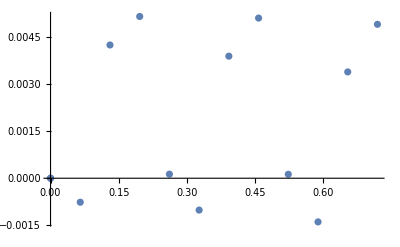

```mathematica
ListPlot[{{0,0},{Pi/48,-0.0007652143662150727},{Pi/24,0.004248287289865201},{Pi/16,0.005157835844825125},{Pi/12,0.0001298416662219695},{(5*Pi)/48,-0.0010156667157836408},{Pi/8,0.0038916999761755586},{(7*Pi)/48,0.0051066397252673285},{Pi/6,0.00012521984513794385},{(3*Pi)/16,-0.0013925706717415052},{(5*Pi)/24,0.0033888093093360503},{(11*Pi)/48,0.0049071771288371315},{0,0}}]
```